## LindbladSolver Documentation

## Preamble

```mathematica
Needs["LindbladSolver`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["QuantumChannel`"]
Needs["QuantumSystems`"]
```

## Introduction and Overview

The LindbladSolver package is a set of functions for numerically or symbolically solving coupled systems of 1st-order ordinary differential equations of the form  x’(t)=A(t).x(t) where x(t) is a d-dimensional vector, and A(t) is a {d,d} dimensional matrix. 

In particular this includes: 
• Schrodinger equations for closed quantum system evolution, where A(t) is a Hamiltonian -i H(t), and x(t) is a state vector |ψ(t)⟩.
• Lindblad equations for open quantum system evolution where A(t) is a Lindblad equation superoperator consisting of Hamiltonian and collapse operator superoperators, and x(t) is a vectorized density matrix |ρ(t)⟩⟩.

## Simulation of First order ODE

### ODE Solver

ODESolver[mat,{init,t0,tf},opts] numerically solves the matrix 1st-order ODE  x’[t] = mat[t].x[t] from time t0 to tf for initial condition x[t0]=init.
mat may be either a matrix, or a pure function of a single variable which evaluates to a matrix, this variable corresponds to t. This is done by calling NDSolveValue, and returns the interpolation function for the coefficients of the vector x. These may be put into the form of a function of time by calling Through[sol[i]] on the solution sol.

ODESolver[mat,{init,t0},opts] attempts to analytically solve the matrix ODE by calling DSolveValue rather than NDSolveValue for initial condition x[t0]=init.
If successful it returns the solution vector x as a function of time.

ODESolver[mat,opts] attempts to analytically solve the matrix ODE by calling DSolveValue without an initial condition. 
If successful it returns the solution vector x as a function of time in terms of constants C[j] which can later be evaluated for different initial conditions.

NDSolveValue and DSolveValue options will be passed to the respective function.
There is an additional option Symbol→sym which allows for specififying a custom symbol to be used for the elements of the vector x in the solution.  The default value is the string “x”.
This can be used to pass custom options to NDSolveValue such as EvaluationMonitor in terms of these coefficients.

#### Utility Functions

ODECoefficients[{d,sym}] yields the list of coefficients {sym[1], sym[2],...,sym[d]}.

ODEVariables[{d,t,sym}] yields the list of time dependent coefficients {sym[1][t],sym[2][t],...,sym[d][t]}.

ODEInitialConditions[init,{t0,sym}] yields the inital condition equation sym[j][t0]==init[[j]] for each component of the vector init.

ODEFirstOrderSystem[mat,{t,sym}] yields the set of first order ODE equations  sym[j]’[t]==mat[[j,1]][t].sym[1][t]+mat[[j,2]][t].sym[2][t] for the matrix mat.

#### Options

Option | Default Value | Description
Symbol | "x" | Symbol is an option for ODESolver that sets the symbol used internally for the ODE coefficients used to set up the system of equations.

DSolveValue options may be used when solving symbolically

Option | Default Value | Description
DependentVariables | Automatic | DependentVariables is an option for NDSolve and other functions that specifies the list of all objects that should be considered as dependent variables in equations that have been supplied.
DiscreteVariables | {} | DiscreteVariables is an option for NDSolve and other functions that specifies variables that only change at discrete times in a temporal integration.
GeneratedParameters | C | GeneratedParameters is an option that specifies how parameters generated to represent the results of various symbolic operations should be named. 
Method | Automatic | Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.

NDSolveValue options may be used when solving numerically.

Option | Default Value | Description
AccuracyGoal | Automatic | AccuracyGoal is an option for various numerical operations which specifies how many effective digits of accuracy should be sought in the final result. 
Compiled | Automatic | Compiled is an option for various numerical and plotting functions which specifies whether the expressions they work with should automatically be compiled. 
DependentVariables | Automatic | DependentVariables is an option for NDSolve and other functions that specifies the list of all objects that should be considered as dependent variables in equations that have been supplied.
DiscreteVariables | {} | DiscreteVariables is an option for NDSolve and other functions that specifies variables that only change at discrete times in a temporal integration.
EvaluationMonitor | None | EvaluationMonitor is an option for various numerical computation and plotting functions that gives an expression to evaluate whenever functions derived from the input are evaluated numerically. 
InterpolationOrder | Automatic | InterpolationOrder is an option for Interpolation, as well as ListLinePlot, ListPlot3D, ListContourPlot, and related functions, that specifies what order of interpolation to use.
MaxStepFraction | 1/10 | MaxStepFraction is an option to functions like NDSolve that specifies the maximum fraction of the total range to cover in a single step.
MaxSteps | Automatic | MaxSteps is an option to functions like NDSolve that specifies the maximum number of steps to take in generating a result.
MaxStepSize | Automatic | MaxStepSize is an option to functions like NDSolve that specifies the maximum size of a single step used in generating a result.
Method | Automatic | Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.
NormFunction | Automatic | NormFunction is an option for functions such as FindFit and NDSolve which gives a function to be minimized in generating results.
PrecisionGoal | Automatic | PrecisionGoal is an option for various numerical operations which specifies how many effective digits of precision should be sought in the final result. 
StartingStepSize | Automatic | StartingStepSize is an option to NDSolve and related functions that specifies the initial step size to use in trying to generate results.
StepMonitor | None | StepMonitor is an option for iterative numerical computation functions that gives an expression to evaluate whenever a step is taken by the numerical method used. 
WorkingPrecision | MachinePrecision | WorkingPrecision is an option for various numerical operations that specifies how many digits of precision should be maintained in internal computations.

#### Example

We can numerically solve an ODE corresponding to schrodingers equaiton with Hamiltonian σ_X for a given inital state {0,1} from time 0 to 2π.

```mathematica
odeSol1=ODESolver[-I*PauliMatrix[1],{{0,1},0,2π}]
```

{InterpolatingFunction[{{0., 6.28319}}, <>],InterpolatingFunction[{{0., 6.28319}}, <>]}

To convert this solution to a function of time we may use the function Through

```mathematica
Through[odeSol1[t]]
```

{InterpolatingFunction[{{0., 6.28319}}, <>][t],InterpolatingFunction[{{0., 6.28319}}, <>][t]}

We plot the populations (squared norm) of the two basis vectors for this evolution

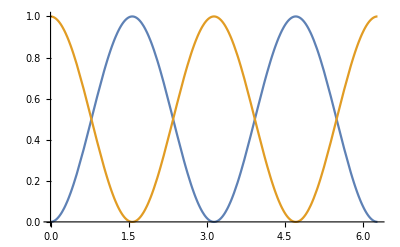

```mathematica
Plot[Evaluate[Abs[Through[odeSol1[t]]]^2],{t,0,2π}]
```

We can solve the previous equation symbolically by not specifying the final time for the evolution.

```mathematica
ODESolver[-I*PauliMatrix[1],{{0,1},0}][t]
```

{-ⅈ Sin[t],Cos[t]}

We can also solve it generally for any initial conditions by not specifying an initial state.

```mathematica
odeSol1sym[t_]=ODESolver[-I*PauliMatrix[1]][t]
```

{C[1] Cos[t]-ⅈ C[2] Sin[t],C[2] Cos[t]-ⅈ C[1] Sin[t]}

The constants in the above solution can then be replaced by different initial conditions.

```mathematica
odeSol1init1=MapThread[Rule,{odeSol1sym[0],{1,0}}]
odeSol1init2=MapThread[Rule,{odeSol1sym[0],{1,I}/Sqrt[2]}]
```

{C[1]→1,C[2]→0}

{C[1]→1/(√2),C[2]→ⅈ/(√2)}

```mathematica
odeSol1sym[t]/.odeSol1init1
odeSol1sym[t]/.odeSol1init2
```

{Cos[t],-ⅈ Sin[t]}

{Cos[t]/(√2)+Sin[t]/(√2),(ⅈ Cos[t])/(√2)-(ⅈ Sin[t])/(√2)}

### Schrodinger’s Equation Solver

SchrodingerSolver[ham,{init,t0,tf},opts] numerically solves the matrix 1st-order ODE  x’[t] = -I*mat[t].x[t] from time t0 to tf for initial condition x[t0]=init.
ham may be either a matrix, or a pure function of a single variable which evaluates to a matrix, this variable corresponds to t. This is done by calling NDSolveValue, and returns the interpolation function for the coefficients of the vector x as a function of t.

SchrodingerSolver[ham,{init,t0},opts] attempts to analytically solve the matrix ODE by calling DSolveValue rather than NDSolveValue for initial condition x[t0]=init.
If successful it returns the solution vector x as a function of time.

SchrodingerSolver[ham,opts] attempts to analytically solve the matrix ODE by calling DSolveValue without an initial condition. 
If successful it returns the solution vector x as a function of time in terms of constants C[j] which can later be evaluated for different initial conditions.

NDSolveValue and DSolveValue options will be passed to the respective function.
There is an additional option Symbol→sym which allows for specififying a custom symbol to be used for the elements of the vector x in the solution.  The default value is the string “x”.
This can be used to pass custom options to NDSolveValue such as EvaluationMonitor in terms of these coefficients.

#### Options

The options to SchrodingerSolver are the same as for ODESolver

#### Example 1 - Single spin with time dependent control field

We can numerically solve an ODE corresponding to schrodingers equaiton with a time dependent Hamiltonian H=σ_z+Cos[t]σ_X for a given inital state {0,1} from time 0 to 10π.

```mathematica
schrodSol1[t_]=SchrodingerSolver[(Spin[Z][1/2]+Cos[#]*Spin[X][1/2])&,{QState[Zm,VectorQ->True],0,10π}][t]
```

{InterpolatingFunction[{{0., 31.4159}}, <>][t],InterpolatingFunction[{{0., 31.4159}}, <>][t]}

We plot the populations (squared norm) of the two basis vectors for this evolution

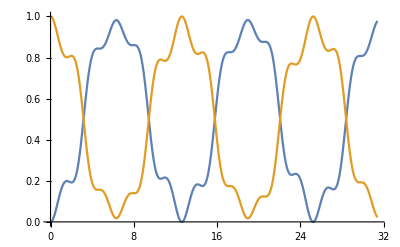

```mathematica
Plot[Evaluate[Abs[schrodSol1[t]]^2],{t,0,10π}]
```

Attempting to solve the previous equation symbolical fails (Mathematica returns the DSolveValue function without evaluation.)

```mathematica
SchrodingerSolver[(PauliMatrix[3]+Cos[#]*PauliMatrix[1])&,{{0,1},0}][t]
```

DSolveValue[x[1]'[t]==-ⅈ x[1][t]-ⅈ Cos[t] x[2][t]&&x[2]'[t]==-ⅈ Cos[t] x[1][t]+ⅈ x[2][t]&&x[1][0]==0&&x[2][0]==1,{x[1][t],x[2][t]},t]

#### Example 2 - Collective coupling of 3-spins to a cavity

We can numerically solve an ODE corresponding to schrodingers equation H=J_+a+J_-a^† where J_± = ∑_(i=1)^3 σ_±^(i) are the collective spin operators, where we truncate the cavity to a 10-dimensional Hilbert space.

```mathematica
ham3=Spin[MII+IMI+IIM][1/2]⊗Cavity[c][10]+Spin[PII+IPI+IIP][1/2]⊗Cavity[a][10];
```

We let each spins initially be in the spins-up state in the Z-direction, and the cavity in the ground state.

```mathematica
init3=QState[ZpZpZp,VectorQ->True]⊗UnitVector[10,1];
```

We now numerically compute the solution for time evolution

```mathematica
schrodSol2[t_]=SchrodingerSolver[ham3,{init3,0,10π}][t];
```

We plot the collective magnetization of the spins and number operator of the cavity

```mathematica
JzExp[t_]=Abs[Conjugate[schrodSol2[t]].(Spin[ZII+IZI+IIZ][1/2]⊗Cavity[I][10]).schrodSol2[t]];
NumExp[t_]=Abs[Conjugate[schrodSol2[t]].(Spin[III][1/2]⊗Cavity[N][10]).schrodSol2[t]];
```

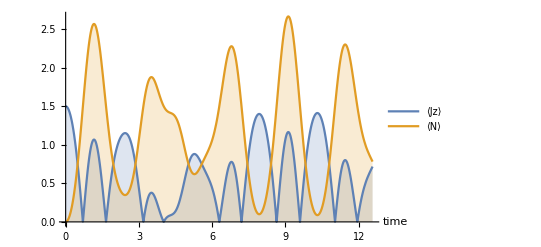

```mathematica
Plot[{JzExp[t],NumExp[t]},{t,0,4π},Filling->Axis,PlotLegends->{"⟨Jz⟩","⟨N⟩"},AxesLabel->{"time",""}]
```

### Lindblad Equation Solver

LindbladSolver[lind,{init,t0,tf},opts] numerically solves the matrix 1st-order ODE  Vec[ρ’[t]] = lind.Vec[ρ[t]] from time t0 to tf for initial condition ρ[t0]=init.
lind may be either a matrix or QuantumChannel, or a pure function of a single variable which evaluates to a matrix or QuantumChannel. This is done by calling NDSolveValue, and returns the interpolation function for the coefficients of the matrix ρ[t] as a function of t.

LindbladSolver[{ham,{c1,c2,...}},{init,t0,tf},opts] calls LindbladSolver for a Lindblad with Hamiltonian term ham, and collapose operators {c1,c2,...}.
ham may be either a matrix, or a pure function of a single variable which evaluates to a matrix, {c1,c2,...} may be a matrices or pure functions of a single variable which evaluate to matrices.

LindbladSolver[lind,{init,t0},opts] and LindbladSolver[{ham,{c1,c2,...}},{init,t0},opts] attempt to analytically solve the matrix ODE by calling DSolveValue rather than NDSolveValue for initial condition ρ[t0]=init. If successful it returns the solution matrix ρ[t] as a function of time.

LindbladSolver[lind,opts] and LindbladSolver[{ham,{c1,c2,...}},opts] attempt to analytically solve the matrix ODE by calling DSolveValue without an initial condition. 
If successful it returns the solution matrix ρ[t] as a function of time in terms of constants C[j] which can later be evaluated for different initial conditions.

NDSolveValue and DSolveValue options will be passed to the respective function.
There is an additional option Symbol→sym which allows for specififying a custom symbol to be used for the elements of the vector x in the solution.  The default value is the string “x”.
This can be used to pass custom options to NDSolveValue such as EvaluationMonitor in terms of these coefficients.

#### Options

The options to LindbladSolver are the same as for ODESolver

#### Example - Collective coupling of 3-spins to a dissipative cavity

We can numerically solve an ODE corresponding to schrodingers equation H=J_+a+J_-a^† where J_± = ∑_(i=1)^3 σ_±^(i) are the collective spin operators, where we truncate the cavity to a 5-dimensional Hilbert space, and the cavity has photon loss dissipator to the ground state.

```mathematica
lind=Lindblad[Spin[MII+IMI+IIM][1/2,SparseArray]⊗Cavity[c][5,SparseArray]+Spin[PII+IPI+IIP][1/2,SparseArray]⊗Cavity[a][5,SparseArray],{Spin[III][1/2,SparseArray]⊗Cavity[a][5,SparseArray]}]
```

Super[SparseArray[<10240>, {1600, 1600}],<params>]

We let each spins initially be in the spins-up state in the Z-direction, and the cavity in the ground state.

```mathematica
init3=Projector[SparseArray[QState[ZpZpZp,VectorQ->True]⊗UnitVector[5,1]]];
KetForm[init3,{2,2,2,5}]
```

|0_2 0_2 0_2 0_5⟩⟨0_2 0_2 0_2 0_5|

We now numerically compute the solution for time evolution

```mathematica
lindSol1[t_]=LindbladSolver[lind,{init3,0,10π}][t];
```

We plot the collective magnetization of the spins and number operator of the cavity

```mathematica
lindJzExp[t_]=Re@Tr[(Spin[ZII+IZI+IIZ][1/2]⊗Cavity[I][5]).lindSol1[t]];
lindNumExp[t_]=Re@Tr[(Spin[III][1/2]⊗Cavity[N][5]).lindSol1[t]];
```

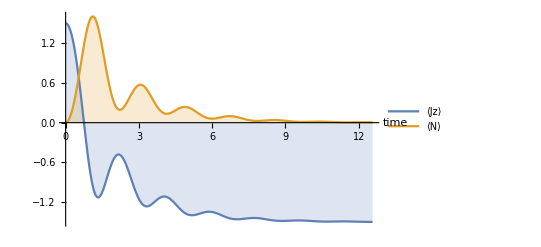

```mathematica
Plot[{lindJzExp[t],lindNumExp[t]},{t,0,4π},Filling->Axis,PlotLegends->{"⟨Jz⟩","⟨N⟩"},AxesLabel->{"time",""}]
```